# Computing the Hamiltonian of the Golden Chain

Code written by Richard Carini
Advised by Wade Bloomquist and Zhenghan Wang
Notebook available for view or download at https://github.com/rdcarini/SeniorProject/

## Initializing the Golden Chain Basis and Information Relevant to the Fibonacci Anyonic Model

In the following, τ is denoted by 2 and the vacuum vector is denoted by 1. GoldenChainBasis[n] returns an ordered basis that contains all admissible labelings of the ring with n spokes.

```mathematica
GoldenChainBasis[1] = {{2,2}} 
GoldenChainBasis[2] = {{1,2,1},{2,1,2},{2,2,2}}
GoldenChainBasis[L_]:=GoldenChainBasis[L]= Module[{PrevChain=GoldenChainBasis[L-1],SecondPrevChain= GoldenChainBasis[L-2],GoldenTemp={}},Do[If[PrevChain[[i]][[2]]==2&&PrevChain[[i]][[1]]==2,AppendTo[GoldenTemp,{Insert[PrevChain[[i]],2, 2],Insert[PrevChain[[i]],1,2]}],AppendTo[GoldenTemp,{Insert[PrevChain[[i]],2, 2]}],Return["Something went wrong"]],{i,1,Length[PrevChain]}];Do[If[SecondPrevChain[[i]][[1]]==1,AppendTo[GoldenTemp,{Flatten[PrependTo[SecondPrevChain[[i]],{1, 2}],1]}],Continue[],Return["Something went wrong"]],{i,1,Length[SecondPrevChain]}];Sort[Flatten[GoldenTemp,1]]]
```

Examples:

```mathematica
GoldenChainBasis[3]
{{1,2,2,1},{2,1,2,2},{2,2,1,2},{2,2,2,2}}
GoldenChainBasis[4]
{{1,2,1,2,1},{1,2,2,2,1},{2,1,2,1,2},{2,1,2,2,2},{2,2,1,2,2},{2,2,2,1,2},{2,2,2,2,2}}
GoldenChainBasis[5]
{{1,2,1,2,2,1},{1,2,2,1,2,1},{1,2,2,2,2,1},{2,1,2,1,2,2},{2,1,2,2,1,2},{2,1,2,2,2,2},{2,2,1,2,1,2},{2,2,1,2,2,2},{2,2,2,1,2,2},{2,2,2,2,1,2},{2,2,2,2,2,2}}
```

Initialize a “Fusion Array” such that FusionArrayFib[[a]][[b]][[c]] returns 1 if the triple (a,b,c) is admissible and 0 otherwise:

```mathematica
FusionArrayFib={{{1,0},{0,1}},{{0,1},{1,1}}}
```

Note that the R moves of the Fibonacci Anyonic model are not explicitly used for the purpose of this thesis, but are included here for completeness.

```mathematica
R[2,2,1]=Exp[4ⅈ Pi/5]
R[2,2,2]=Exp[-3ⅈ Pi/5]
```

VerifyFAdmissibleFib[a,b,c,d,e,f] returns 1 if the F move that contains the corresponding 6-tuple is admissible and 0 otherwise.

```mathematica
VerifyFAdmissibleFib[a_,b_,c_,d_,e_,f_]:=FusionArrayFib⟦a⟧⟦b⟧⟦e⟧ FusionArrayFib⟦c⟧⟦d⟧⟦e⟧ FusionArrayFib⟦b⟧⟦c⟧⟦f⟧ FusionArrayFib⟦a⟧⟦d⟧⟦f⟧
```

FindPositionsFib is a helper function for computing F matrices. Returns an array of all possible tuples {e,f} such that  VerifyFAdmissibleFib[a,b,c,d,e,f] is 1

```mathematica
FindPositionsFib[a_,b_,c_,d_]:=Module[{Positions={}},Do[If[VerifyFAdmissibleFib[a,b,c,d,i,j]==1,AppendTo[Positions,{i,j}]],{i,1,2},{j,1,2}];Return[Positions]]
```

Example:

```mathematica
FindPositionsFib[1,2,2,1] = {{2,1}}
```

#### F Matrices:

```mathematica
FMat[1,2,2,2]= SparseArray[{FindPositionsFib[1,2,2,2][[1]]}->{1},2]
```

SparseArray[<1>, {2, 2}]

```mathematica
FMat[2,1,2,2]= SparseArray[{FindPositionsFib[2,1,2,2][[1]]}->{1},2]
```

SparseArray[<1>, {2, 2}]

```mathematica
FMat[2,2,1,2]= SparseArray[{FindPositionsFib[2,2,1,2][[1]]}->{1},2]
```

SparseArray[<1>, {2, 2}]

```mathematica
FMat[2,2,2,1]= SparseArray[{FindPositionsFib[2,2,2,1][[1]]}->{1},2]
```

SparseArray[<1>, {2, 2}]

```mathematica
FMat[1,1,2,2]= SparseArray[{FindPositionsFib[1,1,2,2][[1]]}->{1},2]
```

SparseArray[<1>, {2, 2}]

```mathematica
FMat[2,1,1,2]= SparseArray[{FindPositionsFib[2,1,1,2][[1]]}->{1},2]
```

SparseArray[<1>, {2, 2}]

```mathematica
FMat[1,2,2,1]= SparseArray[{FindPositionsFib[1,2,2,1][[1]]}->{1},2]
```

SparseArray[<1>, {2, 2}]

```mathematica
FMat[2,2,1,1]= SparseArray[{FindPositionsFib[2,2,1,1][[1]]}->{1},2]
```

SparseArray[<1>, {2, 2}]

```mathematica
FMat[2,2,2,2]= SparseArray[{FindPositionsFib[2,2,2,2][[1]],FindPositionsFib[2,2,2,2][[2]],FindPositionsFib[2,2,2,2][[3]],FindPositionsFib[2,2,2,2][[4]]}->{ ϕ^(-1), ϕ^(-1/2), ϕ^(-1/2),-ϕ^(-1)},2]
```

SparseArray[<4>, {2, 2}]

Example:

```mathematica
MatrixForm[FMat[2,2,2,2]] = ({{1/ϕ, 1/(√ϕ)}, {1/(√ϕ), -1/ϕ}})
```

## Computing the Hamiltonian of the Golden Chain

HamiltonianArray[n] returns a tuple where the first element is an array of all Local Hamiltonians 1-n and the second element is the Total Hamiltonian (the sum of all Local Hamiltonians)

```mathematica
HamiltonianArray[L_]:=HamiltonianArray[L]=Module[{Basis=GoldenChainBasis[L],LocalHamiltonians={},TotalHamiltonian=SparseArray[{},{Length[GoldenChainBasis[L]],Length[GoldenChainBasis[L]]}]},Do[AppendTo[LocalHamiltonians,Table[If[Drop[Basis[[i]],{k+1}]==Drop[Basis[[j]],{k+1}], FMat[Basis[[i]][[k]],2,2,Basis[[i]][[k+2]]][[Basis[[i]][[k+1]]]][[1]]FMat[2,2,Basis[[i]][[k]],Basis[[i]][[k+2]]][[1]][[Basis[[j]][[k+1]]]],0],{i,1,Length[Basis]},{j,1,Length[Basis]}]]; TotalHamiltonian+=LocalHamiltonians[[k]],{k,1,L-1}];
AppendTo[LocalHamiltonians,Table[If[Take[Basis[[i]],{2,L}]==Take[Basis[[j]],{2,L}], FMat[Basis[[i]][[L]],2,2,Basis[[i]][[2]]][[Basis[[i]][[1]]]][[1]]FMat[2,2,Basis[[i]][[L]],Basis[[i]][[2]]][[1]][[Basis[[j]][[1]]]],0],{i,1,Length[Basis]},{j,1,Length[Basis]}]]; TotalHamiltonian+=LocalHamiltonians[[L]];Return[{LocalHamiltonians,TotalHamiltonian}]]
```

Example:

```mathematica
HamiltonianArray[3][[1]][[1]] = ({{0, 0, 0, 0}, {0, 1/ϕ^2, 0, 1/ϕ^(3/2)}, {0, 0, 0, 0}, {0, 1/ϕ^(3/2), 0, 1/ϕ}}) 
HamiltonianArray[3][[1]][[2]] = ({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 1/ϕ^2, 1/ϕ^(3/2)}, {0, 0, 1/ϕ^(3/2), 1/ϕ}}) 
HamiltonianArray[3][[1]][[3]] = ({{1/ϕ^2, 0, 0, 1/ϕ^(3/2)}, {0, 0, 0, 0}, {0, 0, 0, 0}, {1/ϕ^(3/2), 0, 0, 1/ϕ}}) 
HamiltonianArray[3][[2]] = ({{1/ϕ^2, 0, 0, 1/ϕ^(3/2)}, {0, 1/ϕ^2, 0, 1/ϕ^(3/2)}, {0, 0, 1/ϕ^2, 1/ϕ^(3/2)}, {1/ϕ^(3/2), 1/ϕ^(3/2), 1/ϕ^(3/2), 3/ϕ}})
```

### Analysis of Golden Chain Hamiltonians

Easily compute eigenvalues and characteristic polynomials for Level 3:

```mathematica
Roots[FullSimplify[CharacteristicPolynomial[HamiltonianArray[3][[1]][[1]],λ]]==0,λ]//TraditionalForm
Roots[FullSimplify[CharacteristicPolynomial[HamiltonianArray[3][[1]][[2]],λ]]==0,λ]//TraditionalForm
Roots[FullSimplify[CharacteristicPolynomial[HamiltonianArray[3][[1]][[3]],λ]]==0,λ]//TraditionalForm
Roots[FullSimplify[CharacteristicPolynomial[HamiltonianArray[3][[2]],λ]]==0,λ]//TraditionalForm
FullSimplify[CharacteristicPolynomial[HamiltonianArray[3][[2]],λ]/.ϕ->GoldenRatio]//TraditionalForm
```

λ==0∨λ==0∨λ==0∨λ==(ϕ+1)/ϕ^2

λ==0∨λ==0∨λ==0∨λ==(ϕ+1)/ϕ^2

λ==0∨λ==0∨λ==0∨λ==(ϕ+1)/ϕ^2

λ==0∨λ==1/ϕ^2∨λ==1/ϕ^2∨λ==(3 ϕ+1)/ϕ^2

1/2 λ (λ (2 (λ-3) λ+3 (√5-1))-7 √5+15)

Legible/simplified eigensystems for Level 4:

```mathematica
Transpose[Eigensystem[HamiltonianArray[4][[1]][[1]]]]//TraditionalForm
Transpose[Eigensystem[HamiltonianArray[4][[1]][[2]]]]//TraditionalForm
Transpose[Eigensystem[HamiltonianArray[4][[1]][[3]]]]//TraditionalForm
Transpose[Eigensystem[HamiltonianArray[4][[1]][[4]]]]//TraditionalForm
Transpose[ToRadicals[FullSimplify[Eigensystem[HamiltonianArray[4][[2]]]/.ϕ->GoldenRatio]]/.Sqrt[5]->2 Inactive[ϕ]-1//Simplify//Activate]//TraditionalForm
```

(0 | {0,0,0,-√ϕ,0,0,1}
0 | {0,0,-√ϕ,0,0,1,0}
0 | {0,0,0,0,1,0,0}
0 | {0,1,0,0,0,0,0}
1 | {1,0,0,0,0,0,0}
(ϕ+1)/ϕ^2 | {0,0,0,1/(√ϕ),0,0,1}
(ϕ+1)/ϕ^2 | {0,0,1/(√ϕ),0,0,1,0})

(0 | {0,0,0,0,-√ϕ,0,1}
0 | {0,0,0,0,0,1,0}
0 | {0,0,0,1,0,0,0}
0 | {-√ϕ,1,0,0,0,0,0}
1 | {0,0,1,0,0,0,0}
(ϕ+1)/ϕ^2 | {0,0,0,0,1/(√ϕ),0,1}
(ϕ+1)/ϕ^2 | {1/(√ϕ),1,0,0,0,0,0})

(0 | {0,0,0,0,0,-√ϕ,1}
0 | {0,0,0,0,1,0,0}
0 | {0,0,-√ϕ,1,0,0,0}
0 | {0,1,0,0,0,0,0}
1 | {1,0,0,0,0,0,0}
(ϕ+1)/ϕ^2 | {0,0,0,0,0,1/(√ϕ),1}
(ϕ+1)/ϕ^2 | {0,0,1/(√ϕ),1,0,0,0})

(0 | {0,-√ϕ,0,0,0,0,1}
0 | {0,0,0,0,0,1,0}
0 | {-√ϕ,0,0,0,1,0,0}
0 | {0,0,0,1,0,0,0}
1 | {0,0,1,0,0,0,0}
(ϕ+1)/ϕ^2 | {0,1/(√ϕ),0,0,0,0,1}
(ϕ+1)/ϕ^2 | {1/(√ϕ),0,0,0,1,0,0})

```mathematica
({{1, {0,0,0,-1,0,1,0}}, {1, {0,-1,0,0,1,0,0}}, {4-2 ϕ, {√(2 ϕ-3),-1,-√(2 ϕ-3),1,-1,1,0}}, {3, {-2 √(2 ϕ+1),-1,2 √(2 ϕ+1),1,-1,1,0}}, {1/2 (3-√(57-32 ϕ)), {1/4 (4 ϕ+√(57-32 ϕ)-7),-(√(26 ϕ+√(885-328 ϕ)-23))/(4 √2),
1/4 (4 ϕ+√(57-32 ϕ)-7),-(√(26 ϕ+√(885-328 ϕ)-23))/(4 √2),
-(√(26 ϕ+√(885-328 ϕ)-23))/(4 √2),-(√(26 ϕ+√(885-328 ϕ)-23))/(4 √2),1}}, {1/2 (√(57-32 ϕ)+3), {ϕ-1/4 √(57-32 ϕ)-7/4,(√(26 ϕ-√(885-328 ϕ)-23))/(4 √2),
ϕ-1/4 √(57-32 ϕ)-7/4,(√(26 ϕ-√(885-328 ϕ)-23))/(4 √2),
(√(26 ϕ-√(885-328 ϕ)-23))/(4 √2),(√(26 ϕ-√(885-328 ϕ)-23))/(4 √2),1}}, {2 ϕ, {ϕ/2,1/(2 √ϕ),ϕ/2,(√(ϕ-1))/2,1/(2 √ϕ),(√(ϕ-1))/2,1}}})
```

Level 5 Ground State Eigenvector (not simplified; computation time is lengthy):

```mathematica
JordanDecomposition[HamiltonianArray[5][[2]]/.ϕ->GoldenRatio][[1]][[All,11]]/.Sqrt[5]->2 Inactive[ϕ]-1//Simplify//Activate//Simplify//TraditionalForm
```

{(8 (12230683946816 ϕ+1803859384818 √(185-80 ϕ)+4033552206304 √(37-16 ϕ)-978297980501 √5 √(ϕ (21 ϕ-16))-2187540786651 √(ϕ (21 ϕ-16))-298168717513 √5 √(-ϕ (336 ϕ^2-1033 ϕ+592))-666725521123 √(-ϕ (336 ϕ^2-1033 ϕ+592))+7558978384790))/(5 ϕ^9 (142 ϕ+11 √(185-80 ϕ)+25 √(37-16 ϕ)+86) (11142 ϕ+1419 √(185-80 ϕ)+3173 √(37-16 ϕ)+6886)^2),(64 (-5344769637719000 ϕ+77717629388727 √5 √(697-231 ϕ)+173781902363329 √(697-231 ϕ)-809198814841264 √(185-80 ϕ)-1809423557297332 √(37-16 ϕ)+362936515836263 √5 √(5 ϕ+21)+811550720926813 √(5 ϕ+21)+103459128214155 √5 √(-80 ϕ^2-151 ϕ+777)+231341643579717 √(-80 ϕ^2-151 ϕ+777)+22154282726007 √5 √(3696 ϕ^2-19699 ϕ+25789)+49538482168101 √(3696 ϕ^2-19699 ϕ+25789)-3303249298148804))/(5 ϕ^8 (6 ϕ+√(185-80 ϕ)+3 √(37-16 ϕ)-6) (142 ϕ+11 √(185-80 ϕ)+25 √(37-16 ϕ)+86)^2 (11142 ϕ+1419 √(185-80 ϕ)+3173 √(37-16 ϕ)+6886)^2),(16 (21698981718766 ϕ+3306741749129 √(185-80 ϕ)+7394099335089 √(37-16 ϕ)+13410708223460))/(5 ϕ^(29/2) (142 ϕ+11 √(185-80 ϕ)+25 √(37-16 ϕ)+86) (11142 ϕ+1419 √(185-80 ϕ)+3173 √(37-16 ϕ)+6886)^2),(512 (90378238466202 ϕ+13623810789703 √(185-80 ϕ)+30463767038371 √(37-16 ϕ)+55856823215456))/(5 ϕ^7 (6 ϕ+√(185-80 ϕ)+3 √(37-16 ϕ)-6) (142 ϕ+11 √(185-80 ϕ)+25 √(37-16 ϕ)+86)^2 (11142 ϕ+1419 √(185-80 ϕ)+3173 √(37-16 ϕ)+6886)^2),-((32 (421114176267870 ϕ+62881559865951 √(185-80 ϕ)+140607442391489 √(37-16 ϕ)-45189119233101 √5 √(ϕ (21 ϕ-16))-101045942448557 √(ϕ (21 ϕ-16))-13623810789703 √5 √(-ϕ (336 ϕ^2-1033 ϕ+592))-30463767038371 √(-ϕ (336 ϕ^2-1033 ϕ+592))+260262874077958))/(5 ϕ^7 (142 ϕ+11 √(185-80 ϕ)+25 √(37-16 ϕ)+86)^2 (11142 ϕ+1419 √(185-80 ϕ)+3173 √(37-16 ϕ)+6886)^2)),(64 (6869935104966614 ϕ+1035588849661021 √(185-80 ϕ)+2315647064582853 √(37-16 ϕ)+4245853395375444))/(5 ϕ^(33/2) (142 ϕ+11 √(185-80 ϕ)+25 √(37-16 ϕ)+86)^2 (11142 ϕ+1419 √(185-80 ϕ)+3173 √(37-16 ϕ)+6886)^2),(4 (28419026 ϕ+3155231 √(185-80 ϕ)+7055311 √(37-16 ϕ)+17563924))/(5 ϕ^7 (142 ϕ+11 √(185-80 ϕ)+25 √(37-16 ϕ)+86) (11142 ϕ+1419 √(185-80 ϕ)+3173 √(37-16 ϕ)+6886)),(16 (285463503554 ϕ+43502229611 √(185-80 ϕ)+97273942583 √(37-16 ϕ)+176426147744))/(5 ϕ^(11/2) (142 ϕ+11 √(185-80 ϕ)+25 √(37-16 ϕ)+86) (11142 ϕ+1419 √(185-80 ϕ)+3173 √(37-16 ϕ)+6886)^2),(8 (1165932046 ϕ+183972284 √(185-80 ϕ)+411374533 √(37-16 ϕ)+720585633))/(5 ϕ^(11/2) (11142 ϕ+1419 √(185-80 ϕ)+3173 √(37-16 ϕ)+6886)^2),(32 √2 (12 (219602+98209 √5) ϕ^5+10 (294627 √(185-80 ϕ)+658806 √(37-16 ϕ)-5476520 √5-12245871) ϕ^4+(-38819920 √(185-80 ϕ)-86803980 √(37-16 ϕ)+405143294 √5+905927946) ϕ^3+(153213415 √(185-80 ϕ)+342595611 √(37-16 ϕ)-1229418967 √5-2749064383) ϕ^2+(-244321723 √(185-80 ϕ)-546319981 √(37-16 ϕ)+1691242689 √5+3781733619) ϕ+143534203 √(185-80 ϕ)+320952235 √(37-16 ϕ)-857802033 √5-1918103657))/((1+√5)^(9/2) ((58+26 √5) ϕ^2+2 (13 √(185-80 ϕ)+29 √(37-16 ϕ)-83 √5-185) ϕ-31 √(185-80 ϕ)-69 √(37-16 ϕ)+271 √5+605) ((7142+3194 √5) ϕ^4+4 (1597 √(185-80 ϕ)+3571 √(37-16 ϕ)-22968 √5-51358) ϕ^3+(-48376 √(185-80 ϕ)-108172 √(37-16 ϕ)+435850 √5+974590) ϕ^2+2 (57204 √(185-80 ϕ)+127912 √(37-16 ϕ)-387131 √5-865651) ϕ-78431 √(185-80 ϕ)-175377 √(37-16 ϕ)+506851 √5+1133353)),1}

Computational demonstration of accuracy of numerical approximation of eigenvectors:

```mathematica
N[Normalize[Eigensystem[HamiltonianArray[4][[2]]/.ϕ->GoldenRatio,1][[2]][[1]]],50]+Eigensystem[SetPrecision[HamiltonianArray[4][[2]]/.ϕ->GoldenRatio,50],1][[2]][[1]]
```

{0.,0.,0.,0.,0.,0.,0.}

```mathematica
Eigensystem[SetPrecision[HamiltonianArray[5][[2]]/.ϕ->GoldenRatio,50],1][[2]][[1]]
```

{-0.1121335810793403741151909442463732858360485001209,-0.1121335810793403741151909442463732858360485001209,-0.2331896714882209003785501382399952138665971104721,-0.1121335810793403741151909442463732858360485001209,-0.1121335810793403741151909442463732858360485001209,-0.2331896714882209003785501382399952138665971104721,-0.1121335810793403741151909442463732858360485001209,-0.2331896714882209003785501382399952138665971104721,-0.2331896714882209003785501382399952138665971104721,-0.2331896714882209003785501382399952138665971104721,-0.8156244144995250660232581654032578495670598412899}

```mathematica
Eigensystem[N[HamiltonianArray[6][[2]]/.ϕ->GoldenRatio,70],1]
```

{{4.698543184702375097184269638268731492930280361942491536146776470807655},{{-0.4350145462161208784223735774078628506720310631459625738630119703924052,-0.1649340596582949935995487449465231119610825284774200127104566868703353,-0.04338998313486231948417507959024774504021687567550547338001394352638587,-0.1649340596582949935995487449465231119610825284774200127104566868703353,-0.1756882697371335661390338902578241787041722717191723916225628086649081,-0.4350145462161208784223735774078628506720310631459625738630119703924052,-0.1649340596582949935995487449465231119610825284774200127104566868703353,-0.04338998313486231948417507959024774504021687567550547338001394352638587,-0.1649340596582949935995487449465231119610825284774200127104566868703353,-0.1756882697371335661390338902578241787041722717191723916225628086649081,-0.1649340596582949935995487449465231119610825284774200127104566868703353,-0.04338998313486231948417507959024774504021687567550547338001394352638587,-0.1756882697371335661390338902578241787041722717191723916225628086649081,-0.1649340596582949935995487449465231119610825284774200127104566868703353,-0.1756882697371335661390338902578241787041722717191723916225628086649081,-0.1756882697371335661390338902578241787041722717191723916225628086649081,-0.1756882697371335661390338902578241787041722717191723916225628086649081,-0.5171643300730156412851483577929354736618925971896478696066091908162716}}}

## Visualizing Golden Chain Hamiltonian Matrices

In the “Diagrammatic Discussion” of the paper, it was mentioned the potential future work related to analyzing the nonzero entries of the Hamiltonian in hopes of determining an alternative diagrammatic explanation that meaningfully “limits to” the exact form of the Hamiltonian. What follows are lines of Mathematica code whose purpose is to assist in this front.

```mathematica
Manipulate[Show[MatrixPlot[1000*N[HamiltonianArray[a][[2]]/.ϕ->GoldenRatio]],ImageSize->Small],{a,3,11,1}]
```

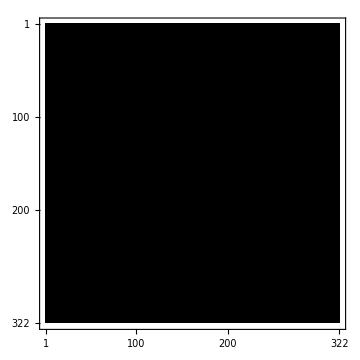

```mathematica
Show[MatrixPlot[N[HamiltonianArray[12][[2]]/.ϕ->GoldenRatio]],ImageSize->Medium]
```

```mathematica
Position[N[HamiltonianArray[8][[2]]/.ϕ->GoldenRatio],Max[N[HamiltonianArray[8][[2]]/.ϕ->GoldenRatio]]]
```

{{1,1},{14,14}}